Cos[x]^2

{1,3/4,1/2,1/4,0}

1

{{1,0,0,0,0},{1,π/6,π^2/36,π^3/216,π^4/1296},{1,π/4,π^2/16,π^3/64,π^4/256},{1,π/3,π^2/9,π^3/27,π^4/81},{1,π/2,π^2/4,π^3/8,π^4/16}}

{{1,0,0,0,0,1},{1,π/6,π^2/36,π^3/216,π^4/1296,3/4},{1,π/4,π^2/16,π^3/64,π^4/256,1/2},{1,π/3,π^2/9,π^3/27,π^4/81,1/4},{1,π/2,π^2/4,π^3/8,π^4/16,0},{1,x,x^2,x^3,x^4,0}}

1+x/(4 π)-(27 x^2)/(2 π^2)+(18 x^3)/π^3

{True,True,True,True,True}

1+x/(4 π)-(27 x^2)/(2 π^2)+(18 x^3)/π^3

True

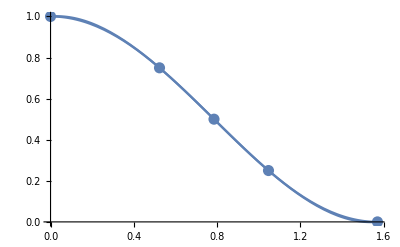

0.000937315

0.115336

```mathematica
f[x_] = Cos[x]^2
X = {0,Pi/6,Pi/4,Pi/3,Pi/2}; F = f[X]
n = Length[X]-1;
Do[{Subscript[x, i] = X[[i + 1]], Subscript[f, i] = F[[i+1]]},{i,0,n}]
Unprotect[Power];0^0=1
V=Table[Subscript[α, i,j]=Subscript[x, i]^j,{i,0,n},{j,0,n}]
Do[{Subscript[α, i,n+1]=Subscript[f, i], Subscript[α, n+1,i]=x^i},{i,0,n}]
Subscript[α, n+1,n+1]=0;
V1=Table[Subscript[α, i,j],{i,0,n+1},{j,0,n+1}]
P[x_]=-Det[V1]/Det[V]//Expand
Table[P[Subscript[x, i]]==Subscript[f, i],{i,0,n}]
Tbl = Table[{Subscript[x, i], Subscript[f, i]},{i,0,n}];
P1[x_] = InterpolatingPolynomial[Tbl,x]//Expand
P[x]==P1[x]
Gr1 = ListPlot[Tbl, PlotStyle->{PointSize[0.02]}];
Gr2 = Plot[P[x], {x,Subscript[x, 0],Subscript[x, n]}];
Gr3 =Plot[f[x], {x,Subscript[x, 0],Subscript[x, n]}];
Show[Gr1,Gr2,Gr3]
Δf = Abs[f[Pi/7] - P[Pi/7]]//N
δf = Abs[(f[Pi/7]-P[Pi/7])/P[Pi/7]]100//N
```

```mathematica
V=Table[{1,Sin[Subscript[t, j]],Cos[Subscript[t, j]]},{j,0,2}]
Det[V]//TrigToExp//Factor
```

{{1,Sin[t_0],Cos[t_0]},{1,Sin[t_1],Cos[t_1]},{1,Sin[t_2],Cos[t_2]}}

-1/2 ⅈ ⅇ^(-ⅈ t_0-ⅈ t_1-ⅈ t_2) (-ⅇ^(ⅈ t_0)+ⅇ^(ⅈ t_1)) (ⅇ^(ⅈ t_0)-ⅇ^(ⅈ t_2)) (ⅇ^(ⅈ t_1)-ⅇ^(ⅈ t_2))